# BigData Optimal Tax: Life-Cycle

This notebook takes the basic life cycle model and examines what happens for many alternative combinations of capital and labor tax rates.

```mathematica
x=0; Remove["Global`*"];
```

Define the main life-cycle constants, the utility function, and the age-wage path.

```mathematica
startTime = TimeObject[Now];
Needs["IPOPTLink`"]
ParallelNeeds["IPOPTLink`"]
```

c^(1-γ)/(1-γ)-(B l^(1+η))/(1+η)

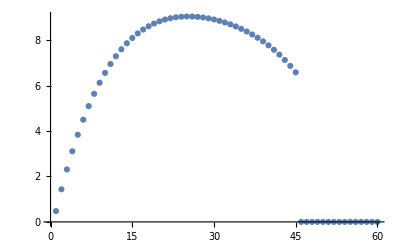

```mathematica
T=60;Tret=45;
r=0.1;R=1 + r; 
β=.95;
u[c_,l_] =c^(1-γ)/(1-γ)-B l^(1+η)/(1+η)
(* Specify age-wage path*)
Do[w[t]=-36.9994+3.52022(t+17)-.101878(t+17)^2+.00134816(t+17)^3-7.06233*10^-6(t+17)^4,{t,1,Tret}];
wagelist=Table[If[i≤ Tret,w[i],0],{i,T}];
ListPlot[wagelist]
```

We define the basic optimization problem.

```mathematica
Tax[capInc_,labInc_]=τK (R-1) capInc   +τL labInc;
PVrevL= Sum[τL w[t] l[t] R^(-t+1),{t,1,Tret}] ;
PVrevK= Sum[τK (R-1) a[t] R^(-t+1),{t,1,T}] ;
PVrevC= Sum[τC c[t] R^(-t+1),{t,1,T}] ;
```

```mathematica
obj = Sum[β^(t-1) u[c[t],l[t]],{t,1,T}];
(*Define Budget Constraints*)
bc1=Table[(R  a[t]+w[t] l[t]-c[t]-Tax[ a[t],w[t] l[t]])-a[t+1]≥ 0,{t,1,T}];
(*Define bound Constraints*)
bcaT={a[T+1]≥ 0};
abnds=Table[a[t]≥ amin,{t,2,T}];
lbndsc=Table[c[t]≥ 0.0001,{t,1,T}];
lbndsl=Map[#≥0&,Table[l[t],{t,1,Tret}]]; 
{vars,varbounds} = (Union[abnds,bcaT,lbndsc,lbndsl ]/.{( a_≥ b_  ) -> {a,b,∞}}//Transpose)/. {v_,lb_,ub_}:> {v,Transpose[{lb,ub}]};

constraintsToIntervals= 
{
	( a_== b_  ) -> LessEqual[0,a-b,0],
	( a_ <=  b_ ) -> LessEqual[-∞,a-b,0],
	(a_ >= b_  ) -> LessEqual[0,a-b,∞]
};
ipoptConstraintStyle= LessEqual[lb_,v_,ub_]-> {v,{lb,ub}} ;
{budgetconstraintfunctions,budgetconstraintvals} = Transpose[bc1 /.constraintsToIntervals/.ipoptConstraintStyle ];
```

```mathematica
(*Set initial guess for all variables to be 1; probably not a feasible point but better than letting them be zero.*)
varsinit=Table[1,Length[vars]];
```

```mathematica
(*Define border conditions particular to the problem*)
a[1]=0;
Do[ l[i]=0,{i,Tret+1,T}];
```

This is the command which takes as input the tax rates, the borrowing constraints, and preference parameters, and outputs the individuals utility and solution path.

NOTE: This is a very simple problem. One should think of f[----] as a black box because it will often be a substantive computation on its own. In this notebook I do nothing that relies on special features of this problem. I use this problem because it is fast to compute, and it allows me to demonstrate the general concept of computing a Pareto frontier.

```mathematica
f[{τK0_,τL0_,amin0_,γ0_,η0_,B0_}] :=Module[{ipoptOut,sol,utility,solRule,PVrevK0,PVrevL0},
pfun  = ParametricIPOPTMinimize[-obj,
							vars,
							varsinit,
							varbounds,
							budgetconstraintfunctions,
							budgetconstraintvals,
							{τK,τL,amin,γ,η,B}];
ipoptOut = pfun[τK0,τL0,amin0,γ0,η0,B0];
sol = IPOPTArgMin[ipoptOut];
utility = -IPOPTMinValue[ipoptOut];
solRule = Join[MapThread[Rule,{vars,sol}],{τK->τK0,τL->τL0}];
PVrevK0=PVrevK/.solRule;PVrevL0=PVrevL/.solRule;
{utility,PVrevK0+PVrevL0, PVrevK0,PVrevL0,τK0,τL0}];
```

Here is a simple example

```mathematica
f[{.4,.5,-3000,0.5,1,1}]//AbsoluteTiming
```

{0.192776,{62.7419,39.3704,-4.45626,43.8267,0.4,0.5}}

## Create Database

Build your database (or import it if already built)

```mathematica
gamlist={1/2,9/10};
etalist={1};
```

```mathematica
tkmax=0.4; tlmax=0.4;
```

```mathematica
dtk=0.005; dtl=0.005;
```

```mathematica
ntk=tkmax/dtk+1
ntl=tlmax/dtl + 1
```

81.

81.

We next evaluate many combinations of taxes for different preferences

{tk, 0, .50, .05} ({tl, 0, .50, .05}) says that we look at tk (tl) beginning with 0 and increasing to 0.50 in steps of 0.05

{aamin,{0}} says we impose a zero lower bound on assets (meaning no borrowing allowed)

{gam,gamlist} and {eeta,etalist} means that gam is drawn from gamlist and eeta is drawn from etalist

```mathematica
parameterSpace = ParallelTable[{tk,tl,aamin,gam,eeta,n},{tk,0,tkmax,dtk},{tl,0,tlmax,dtl},{aamin,{0}},{gam,gamlist},{eeta,etalist},{n,{1}}];
data = ParallelMap[f,parameterSpace,{Depth[parameterSpace]-2}];//Timing
```

{12.0938,Null}

```mathematica
time=%[[1]];
```

We compute how much time is spent on each example

```mathematica
numcases=Length[gamlist] Length[etalist] ntk ntl
time/numcases
```

13122.

0.000921639

output data

```mathematica
data>> dataoutMay2;
```

Next, we read the file

```mathematica
Clear[data]
data=<<dataoutMay2;
```

## The Pareto frontier - tables

In this notebook we care about utility versus revenue. I look forward to higher-dimensional frontiers.

Define Pareto function and Pareto frontier

Function h receives:
	Data in from database of cases
	Target revenue
	Indices - γind and ηind - indicating preference parameters

Function h outputs the optimal element for that revenue, and the policies that produced that outcome.

```mathematica
h[data_,revenue_, alimind_,γind_,ηind_]:=Module[
{dataflat,util,comb},
dataflat=Flatten[data[[All,All,alimind,γind,ηind,1]],1];
util=Max[Select[dataflat,#[[2]]≥revenue&][[All,1]]];
comb=Select[dataflat,#[[1]]==util&]
]
```

```mathematica
casesprefs=Table[{gamlist[[gam]],etalist[[eeta]]},{gam,1,Length[gamlist]},{eeta,1,Length[etalist]}];
casesprefs=Flatten[casesprefs,1];
```

```mathematica
cases=Table[{1,gam,eeta},{gam,1,Length[gamlist]},{eeta,1,Length[etalist]}];
cases=Flatten[cases,1];
```

```mathematica
numcases=Length[cases];
count=0;
```

```mathematica
outcmd:= (count=count+1;
{i,j,k}=cases[[count]];
Print["gamma = ",casesprefs[[count]][[1]],",   eta = ",casesprefs[[count]][[2]]]
maxrev=Transpose[Flatten[data[[All,All,i,j,k,1]],1]][[2]]//Max;
tb=Table[h[data,rev,i,j,k][[1]],{rev,0,0.99 maxrev ,0.04 maxrev}];
TableForm[tb,TableHeadings->{{},{"util","revtot","revk","revl","tk","tl"}}])
```

```mathematica
outcmdold:= (
count=count+1;
{i,j,k}=cases[[count]];
Print["gamma = ",casesprefs[[count]][[1]],",   eta = ",casesprefs[[count]][[2]]]
maxrev=Transpose[Flatten[data[[All,All,i,j,k,1]],1]][[2]]//Max;
Table[h[data,rev,i,j,k][[1]],{rev,0,0.96 maxrev ,0.02 maxrev}]//TableForm)
```

```mathematica
outcmd
```

gamma = 1/2,   eta = 1

| util | revtot | revk | revl | tk | tl
 | 116.907 | 0. | 0. | 0. | 0. | 0.
 | 115.735 | 1.87522 | 0. | 1.87522 | 0. | 0.015
 | 114.443 | 3.82448 | 3.20301 | 0.621466 | 0.02 | 0.005
 | 113.25 | 5.75684 | 0.810358 | 4.94648 | 0.005 | 0.04
 | 112.068 | 7.55933 | 0.793519 | 6.76581 | 0.005 | 0.055
 | 110.774 | 9.48339 | 1.53401 | 7.94938 | 0.01 | 0.065
 | 109.586 | 11.2325 | 1.50128 | 9.73125 | 0.01 | 0.08
 | 108.223 | 13.1382 | 2.86433 | 10.2738 | 0.02 | 0.085
 | 106.95 | 15.022 | 0. | 15.022 | 0. | 0.125
 | 105.579 | 16.9149 | 1.39349 | 15.5215 | 0.01 | 0.13
 | 104.078 | 18.9683 | 0. | 18.9683 | 0. | 0.16
 | 102.836 | 20.6224 | 0. | 20.6224 | 0. | 0.175
 | 101.167 | 22.792 | 0. | 22.792 | 0. | 0.195
 | 99.9062 | 24.3918 | 0. | 24.3918 | 0. | 0.21
 | 98.2128 | 26.4875 | 0. | 26.4875 | 0. | 0.23
 | 96.5047 | 28.5393 | 0. | 28.5393 | 0. | 0.25
 | 95.2136 | 30.0486 | 0. | 30.0486 | 0. | 0.265
 | 93.5327 | 31.8573 | 2.64422 | 29.2131 | 0.025 | 0.26
 | 91.8398 | 33.7236 | 2.54936 | 31.1742 | 0.025 | 0.28
 | 90.0941 | 35.6208 | 1.98506 | 33.6357 | 0.02 | 0.305
 | 88.3096 | 37.4792 | 1.44643 | 36.0327 | 0.015 | 0.33
 | 86.4262 | 39.3623 | 0.471942 | 38.8904 | 0.005 | 0.36
 | 84.3853 | 41.2316 | 1.74147 | 39.4901 | 0.02 | 0.37
 | 82.4136 | 43.044 | 0.849076 | 42.1949 | 0.01 | 0.4
 | 79.6303 | 45.0575 | 3.61091 | 41.4466 | 0.05 | 0.4

## The Pareto frontier - graphs

### Plot all data

We plot all the data points in revenue-utility space. This helps us see where the good points are. I also use colors to indicate the policies.

plot

```mathematica
tmax=Max[tkmax,tlmax]
```

0.4

```mathematica
plot[alimind_,γind_,ηind_]:=Module[

{alimi=alimind,γi=γind,ηi=ηind,Βi=1,dots,colorF,gra1,gra2,plotLegend,leg},

dots=Flatten[data[[All,All,alimi,γi,ηi,Βi]],1];

colorF=Blend[{{0,Green},{tmax,Red}},#]&;

gra1=Graphics[
{{colorF[#5],Tooltip[Point[{#2,#1}],{#5,#6}]}&@@@dots,Text["τK",{Max[dots[[All,2]]]/2,Max[dots[[1,1]]]},{0,-1}]},
Frame->{{True,False},{True,False}}, 
PlotRange->All,
AxesOrigin->{0,0},
FrameLabel-> {"Total Tax Revenue","Consumer Utility"},
ImageSize->Medium,
AxesOrigin-> {0,0}];

gra2=Graphics[{{colorF[#6],Tooltip[Point[{#2,#1}],{#5,#6}]}&@@@dots,Text["τL",{Max[dots[[All,2]]]/2,Max[dots[[1,1]]]},{0,-1}]},Frame->{{True,False},{True,False}}, PlotRange->All,AxesOrigin->{0,0},FrameLabel->{"Total Tax Revenue","Consumer Utility"},ImageSize->Medium,AxesOrigin-> {0,0}];

plotLegend[{min_,max_},n_,col_]:=Graphics[MapIndexed[{{col[#1],Rectangle[{0,#2[[1]]-1},{1,#2[[1]]}]},{Black,Text[NumberForm[N@#1,{4,2}],{4,#2[[1]]-.5},{1,0}]}}&,Rescale[Range[n],{1,n},{min,max}]],Frame->True,FrameTicks->None,PlotRangePadding->.5];

leg=plotLegend[{0,0.8},20,colorF];
Grid[{{Row[{"γ= ",gamlist[[γi]], ", η= ",etalist[[ηi]] , ", Borrowinglimit= ",Piecewise[{{-(alimi-1)*10,alimi<4},{-50,alimi==4}},-∞]}],SpanFromLeft},{gra1,gra2,leg}},ItemSize->Automatic]
]
```

```mathematica
count=0;
```

```mathematica
prntcmd:=(
count=count+1;
{i,j,k}=cases[[count]];
Print["gamma = ",casesprefs[[count]][[1]],",   eta = ",casesprefs[[count]][[2]]];
plot[i,j,k])
```

Each plot is a point in utility-revenue space. The left one uses color to indicate the size of the capital income tax; the right one does so for the labor income tax.
Note that there are some red points in the τL graph that are on the frontier, but the red points in the τK graph are all inferior.

gamma = 1/2,   eta = 1

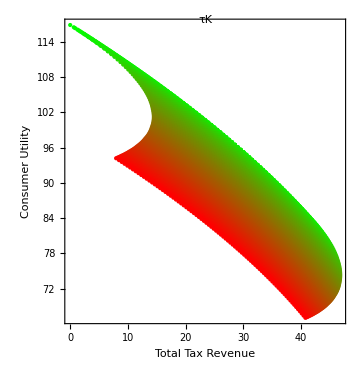
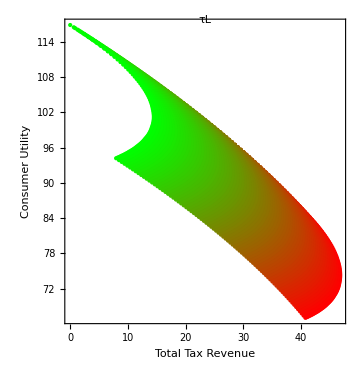
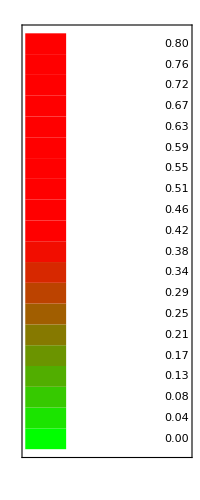
γ= 1/2, η= 1, Borrowinglimit= 0 |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
prntcmd
```

gamma = 9/10,   eta = 1

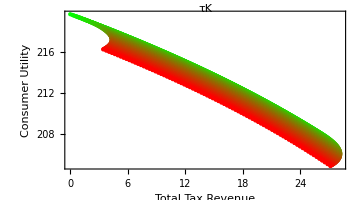
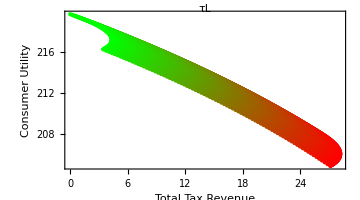
γ= 9/10, η= 1, Borrowinglimit= 0 |  | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
prntcmd
```

```mathematica
TimeObject[Now]- startTime
```

3.39233 min